# Homework 1

## By Marvyn Bailly

## Question 4

{{-2,2},{{-1/(√3),1},{√3,1}}}

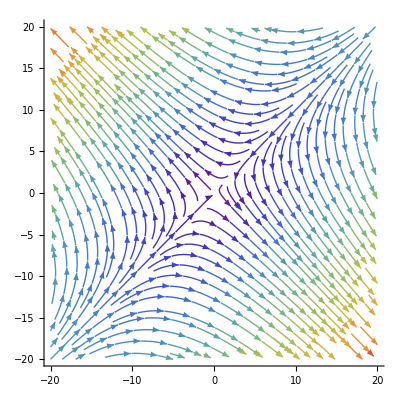

```mathematica
Eigensystem[{{1, Sqrt[3]},{Sqrt[3],-1}}]
StreamPlot[{x-2y,-2x+y},{x,-20,20},{y,-20,20},StreamColorFunction->"Rainbow",Axes -> True,Frame->False, StreamPoints->Fine]
```

## Question 8

Define the system

```mathematica
f[x_,y_] := -(x-y)(1-x-y);
g[x_,y_] := x(2 + y);
F[x_,y_] := {f[x,y],g[x,y]};
MatrixForm[F[x,y]]
```

((1-x-y) (-x+y)
x (2+y))

Find the fixed points

```mathematica
fpList = Solve[{F[x,y][[1]] == 0, F[x,y][[2]] == 0},{x,y}]
```

{{x→-2,y→-2},{x→0,y→0},{x→0,y→1},{x→3,y→-2}}

Define the Jacobian of the system

```mathematica
Clear[x,y];
J[x_,y_] := Transpose[{Derivative[1,0][F][x,y],Derivative[0,1][F][x,y]}] 
MatrixForm[J[x,y]]
```

(-1+2 x | 1-2 y
2+y | x)

Evaluate Jacobian at fixed points and get the corresponding eigensystem.

```mathematica
For[i = 1, i <= Length[fpList],i++,
fp = {fpList[[i]][[1]][[2]],fpList[[i]][[2]][[2]]};
Print[fp];
Print[MatrixForm[J[fp[[1]],fp[[2]]]]];
Print[CharacteristicPolynomial[J[fp[[1]],fp[[2]]],λ]];
Print[Eigensystem[J[fp[[1]],fp[[2]]]]]]
```

{-2,-2}

(-5 | 5
0 | -2)

10+7 λ+λ^2

{{-5,-2},{{1,0},{5,3}}}

{0,0}

(-1 | 1
2 | 0)

-2+λ+λ^2

{{-2,1},{{-1,1},{1,2}}}

{0,1}

(-1 | -1
3 | 0)

3+λ+λ^2

{{1/2 (-1+ⅈ √11),1/2 (-1-ⅈ √11)},{{1/6 (-1+ⅈ √11),1},{1/6 (-1-ⅈ √11),1}}}

{3,-2}

(5 | 5
0 | 3)

15-8 λ+λ^2

{{5,3},{{1,0},{-5,2}}}

Plot the behavior

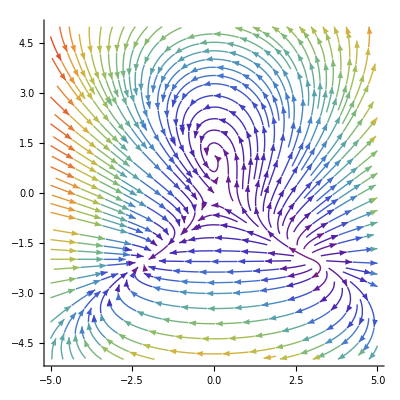

```mathematica
StreamPlot[F[x,y],{x,-5,5},{y,-5,5},StreamColorFunction->"Rainbow",Axes -> True,Frame->False, StreamPoints->Fine]
```

## Question 9

Define the system

```mathematica
f[x_,y_] := x - y^2;
g[x_,y_] := y - x^2;
F[x_,y_] := {f[x,y],g[x,y]};
MatrixForm[F[x,y]]
```

(x-y^2
-x^2+y)

Find the fixed points

```mathematica
fpList = Solve[{F[x,y][[1]] == 0, F[x,y][[2]] == 0},{x,y}]
```

{{x→0,y→0},{x→1,y→1},{x→-(-1)^(1/3),y→(-1)^(2/3)},{x→(-1)^(2/3),y→-(-1)^(1/3)}}

Define the Jacobian of the system

```mathematica
Clear[x,y];
J[x_,y_] := Transpose[{Derivative[1,0][F][x,y],Derivative[0,1][F][x,y]}] 
MatrixForm[J[x,y]]
```

(1 | -2 y
-2 x | 1)

Evaluate Jacobian at fixed points and get the corresponding eigensystem.

```mathematica
For[i = 1, i <= Length[fpList],i++,
fp = {fpList[[i]][[1]][[2]],fpList[[i]][[2]][[2]]};
Print[fp];
Print[MatrixForm[J[fp[[1]],fp[[2]]]]];
Print[CharacteristicPolynomial[J[fp[[1]],fp[[2]]],λ]];
Print[Eigensystem[J[fp[[1]],fp[[2]]]]]]
```

{0,0}

(1 | 0
0 | 1)

1-2 λ+λ^2

{{1,1},{{0,1},{1,0}}}

{1,1}

(1 | -2
-2 | 1)

-3-2 λ+λ^2

{{3,-1},{{-1,1},{1,1}}}

{-(-1)^(1/3),(-1)^(2/3)}

(1 | -2 (-1)^(2/3)
2 (-1)^(1/3) | 1)

-3-2 λ+λ^2

{{3,-1},{{-(-1)^(2/3),1},{(-1)^(2/3),1}}}

{(-1)^(2/3),-(-1)^(1/3)}

(1 | 2 (-1)^(1/3)
-2 (-1)^(2/3) | 1)

-3-2 λ+λ^2

{{3,-1},{{(-1)^(1/3),1},{-(-1)^(1/3),1}}}

Plot the behavior

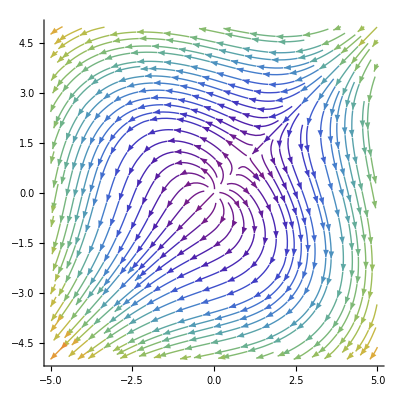

```mathematica
StreamPlot[F[x,y],{x,-5,5},{y,-5,5},StreamColorFunction->"Rainbow",Axes -> True,Frame->False, StreamPoints->Fine]
```

## Question 10

Define the system

```mathematica
f[x_,y_] := (2+x)(y-x);
g[x_,y_] := (4-x)(y+x);
F[x_,y_] := {f[x,y],g[x,y]};
MatrixForm[F[x,y]]
```

((2+x) (-x+y)
(4-x) (x+y))

Find the fixed points

```mathematica
fpList = Solve[{F[x,y][[1]] == 0, F[x,y][[2]] == 0},{x,y}]
```

{{x→-2,y→2},{x→0,y→0},{x→4,y→4}}

Define the Jacobian of the system

```mathematica
Clear[x,y];
J[x_,y_] := Transpose[{Derivative[1,0][F][x,y],Derivative[0,1][F][x,y]}] 
MatrixForm[J[x,y]]
```

(-2-2 x+y | 2+x
4-2 x-y | 4-x)

Evaluate Jacobian at fixed points and get the corresponding eigensystem.

```mathematica
For[i = 1, i <= Length[fpList],i++,
fp = {fpList[[i]][[1]][[2]],fpList[[i]][[2]][[2]]};
Print[fp];
Print[MatrixForm[J[fp[[1]],fp[[2]]]]];
Print[CharacteristicPolynomial[J[fp[[1]],fp[[2]]],λ]];
Print[Eigensystem[J[fp[[1]],fp[[2]]]]]]
```

{-2,2}

(4 | 0
6 | 6)

24-10 λ+λ^2

{{6,4},{{0,1},{-1,3}}}

{0,0}

(-2 | 2
4 | 4)

-16-2 λ+λ^2

{{1+√17,1-√17},{{1/4 (-3+√17),1},{1/4 (-3-√17),1}}}

{4,4}

(-6 | 6
-8 | 0)

48+6 λ+λ^2

{{-3+ⅈ √39,-3-ⅈ √39},{{-1/8 ⅈ (3 ⅈ+√39),1},{1/8 ⅈ (-3 ⅈ+√39),1}}}

Plot the behavior

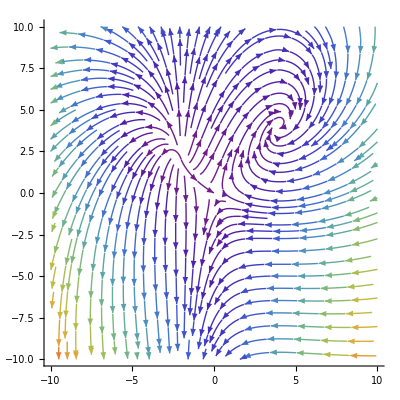

```mathematica
StreamPlot[F[x,y],{x,-10,10},{y,-10,10},StreamColorFunction->"Rainbow",Axes -> True,Frame->False, StreamPoints->Fine]
```